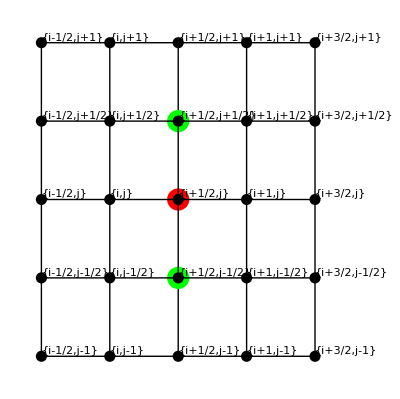

```mathematica
points=Table[{i,j},{i,1,3,.5},{j,1,3,.5}];

grid=Join[Map[Line/@Partition[#,2,1]&,points],Map[Line/@Partition[#,2,1]&,Transpose[points]]];

labelsCenter={3,3};
labelsSizes={3,2};
labelsVars={i+.5,j};

labels=Rationalize@Map[Thread[labelsVars+(#-points[[Sequence@@labelsCenter]])]&,points,{2}];

crossStencil={{0,1},{0,-1}};

Graphics[{Green,PointSize[0.04],Point@Map[points[[Sequence@@(labelsCenter+#)]]&,crossStencil],Red,Point[points[[Sequence@@labelsCenter]]],Black,grid,PointSize[0.02],Map[Point,points,{-2}],MapThread[Text[##,-{1.5,2}]&,Flatten[#,1]&/@{labels,points}]}]
```

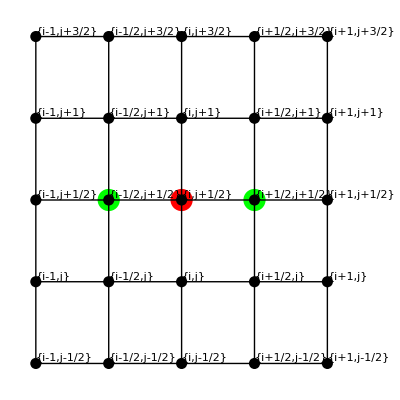

```mathematica
points=Table[{i,j},{i,1,3,.5},{j,1,3,.5}];

grid=Join[Map[Line/@Partition[#,2,1]&,points],Map[Line/@Partition[#,2,1]&,Transpose[points]]];

labelsCenter={3,3};
labelsSizes={3,2};
labelsVars={i,j+.5};

labels=Rationalize@Map[Thread[labelsVars+(#-points[[Sequence@@labelsCenter]])]&,points,{2}];

crossStencil={{1,0},{-1,0}};

Graphics[{Green,PointSize[0.04],Point@Map[points[[Sequence@@(labelsCenter+#)]]&,crossStencil],Red,Point[points[[Sequence@@labelsCenter]]],Black,grid,PointSize[0.02],Map[Point,points,{-2}],MapThread[Text[##,-{1.5,2}]&,Flatten[#,1]&/@{labels,points}]}]
```

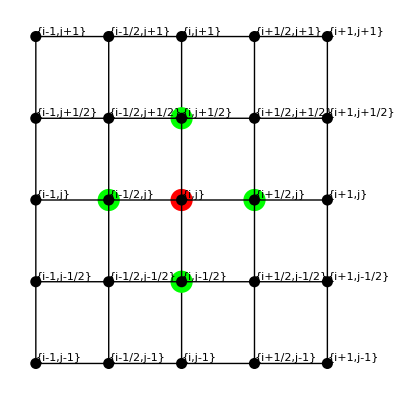

```mathematica
points=Table[{i,j},{i,1,3,.5},{j,1,3,.5}];

grid=Join[Map[Line/@Partition[#,2,1]&,points],Map[Line/@Partition[#,2,1]&,Transpose[points]]];

labelsCenter={3,3};
labelsSizes={3,2};
labelsVars={i,j};

labels=Rationalize@Map[Thread[labelsVars+(#-points[[Sequence@@labelsCenter]])]&,points,{2}];

crossStencil={{1,0},{-1,0},{0,1},{0,-1}};

Graphics[{Green,PointSize[0.04],Point@Map[points[[Sequence@@(labelsCenter+#)]]&,crossStencil],Red,Point[points[[Sequence@@labelsCenter]]],Black,grid,PointSize[0.02],Map[Point,points,{-2}],MapThread[Text[##,-{1.5,2}]&,Flatten[#,1]&/@{labels,points}]}]
```

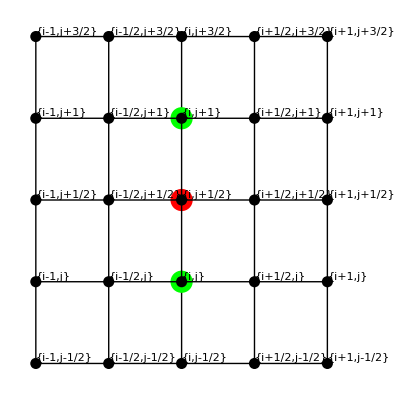

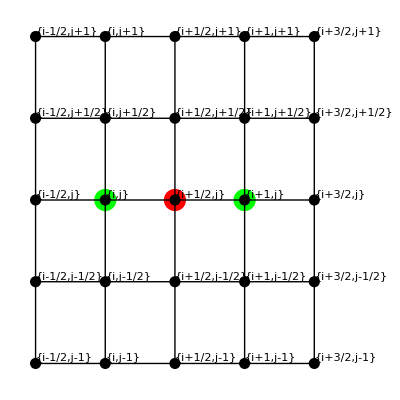

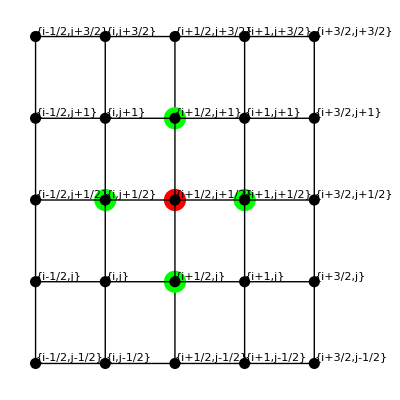

```mathematica
points=Table[{i,j},{i,1,3,.5},{j,1,3,.5}];

grid=Join[Map[Line/@Partition[#,2,1]&,points],Map[Line/@Partition[#,2,1]&,Transpose[points]]];

labelsCenter={3,3};
labelsSizes={3,2};
labelsVars={i,j+.5};

labels=Rationalize@Map[Thread[labelsVars+(#-points[[Sequence@@labelsCenter]])]&,points,{2}];

crossStencil={{0,1},{0,-1}};

Graphics[{Green,PointSize[0.04],Point@Map[points[[Sequence@@(labelsCenter+#)]]&,crossStencil],Red,Point[points[[Sequence@@labelsCenter]]],Black,grid,PointSize[0.02],Map[Point,points,{-2}],MapThread[Text[##,-{1.5,2}]&,Flatten[#,1]&/@{labels,points}]}]


points=Table[{i,j},{i,1,3,.5},{j,1,3,.5}];

grid=Join[Map[Line/@Partition[#,2,1]&,points],Map[Line/@Partition[#,2,1]&,Transpose[points]]];

labelsCenter={3,3};
labelsSizes={3,2};
labelsVars={i+.5,j};

labels=Rationalize@Map[Thread[labelsVars+(#-points[[Sequence@@labelsCenter]])]&,points,{2}];

crossStencil={{1,0},{-1,0}};

Graphics[{Green,PointSize[0.04],Point@Map[points[[Sequence@@(labelsCenter+#)]]&,crossStencil],Red,Point[points[[Sequence@@labelsCenter]]],Black,grid,PointSize[0.02],Map[Point,points,{-2}],MapThread[Text[##,-{1.5,2}]&,Flatten[#,1]&/@{labels,points}]}]




points=Table[{i,j},{i,1,3,.5},{j,1,3,.5}];

grid=Join[Map[Line/@Partition[#,2,1]&,points],Map[Line/@Partition[#,2,1]&,Transpose[points]]];

labelsCenter={3,3};
labelsSizes={3,2};
labelsVars={i+.5,j +.5};

labels=Rationalize@Map[Thread[labelsVars+(#-points[[Sequence@@labelsCenter]])]&,points,{2}];

crossStencil={{0,1},{0,-1},{1,0},{-1,0}};

Graphics[{Green,PointSize[0.04],Point@Map[points[[Sequence@@(labelsCenter+#)]]&,crossStencil],Red,Point[points[[Sequence@@labelsCenter]]],Black,grid,PointSize[0.02],Map[Point,points,{-2}],MapThread[Text[##,-{1.5,2}]&,Flatten[#,1]&/@{labels,points}]}]
```